### Basic data import & manipulation

```mathematica
classicdatapath=FileNameJoin[{"surveydata","classical"}];

(* Import NPY array as List *)
ImportNPY[file_]:=Module[{a,f=OpenRead[file,BinaryFormat->True],version,headerlen,header,dims,type,typ,byto},a=If[BinaryRead[f,"Byte"]==147&&BinaryReadList[f,"Character8",5]==Characters["NUMPY"],version=BinaryReadList[f,"Byte",2];
headerlen=BinaryRead[f,"Integer16",ByteOrdering->-1];
header=StringJoin@BinaryReadList[f,"Character8",headerlen];
dims=StringCases[header,"'shape':"~~Whitespace~~"("~~s:{NumberString,",",Whitespace}..~~")":>ToExpression["{"~~If[StringTake[s,-1]==",",StringDrop[s,-1],s]~~"}"]][[1]];
type=StringCases[header,"'descr':"~~Whitespace~~Shortest["'"~~s:_...~~"'"]:>s][[1]];
byto=Switch[StringTake[type,1],"<",-1,">",1,_,$ByteOrdering];
If[MemberQ[{"<",">","|","="},StringTake[type,1]],type=StringDrop[type,1]];
typ=Switch[type,"f8","Real64","i8","Integer64",_,Print["unknown type",header];0];
If[typ≠0,ArrayReshape[BinaryReadList[f,typ,ByteOrdering->byto],dims],0],Print["not a npy"];0];
Close[f];a];

(* Imports results of optimization for sequences of length l and dimension d;
Outputs a list data such that:
data[[i,1]]: i-th sequence number (0 = 00...00, 1 = 00...01, 2 = 00...10, etc.):
data[[i,2]]: i-th sequence as a pattern, a list such as {0,1,0,1,1}
data[[i,3]]: the best proViewSequence[seq_]:=ArrayPlot[{seq},ColorRules->{0->Hue[0,0,0.9],1->Black},Mesh->All,ImageSize->100,Frame->None];bability encountered via optimization 
(The files results*.txt contain redundant information so they are legible directly)
*)
ImportResults[l_,d_,s_:2]:=Module[{fn,dat},
fn=FileNameJoin[{NotebookDirectory[],classicdatapath,"results_S"<>ToString[s]<>"_L"<>StringPadLeft[ToString[l],2,"0"]<>"_D"<>StringPadLeft[ToString[d],2,"0"]<>".txt"}];
If[FileExistsQ[fn],
dat=Import[fn,"Table"];
dat[[All,2]]=IntegerDigits[#,2,l]&/@dat[[All,1]];
dat,
Print["No data for "<>FileBaseName[fn]<>".txt"]; Abort[];
]
];

(* Import NPY model tensor for a given sequence seq with dimension d and s symbols;
Returns a s×d×d tensor T as a list, so that T0 = T[[1]] *)
ImportTModel[seq0_,d_:2,s_:2]:=Quiet@Module[{t,i,l,fn,seq},l=Length[seq0];
seq=If[seq0[[1]]==1,1-seq0,seq0];
fn=FileNameJoin[{NotebookDirectory[],classicdatapath,"T_S"<>ToString[s]<>"_L"<>StringPadLeft[ToString[l],2,"0"]<>"_D"<>StringPadLeft[ToString[Max[1,d]],2,"0"]<>"_"<>Map[ToString,seq]<>".npy"}];If[FileExistsQ[fn],t=ImportNPY[fn];For[i=1,i≤d,i++,t[[All,i,All]]/=Total@Flatten[t[[All,i,All]]]];t,
Print["No data for "<>FileBaseName[fn]<>".txt"];Abort[];
]];

(* Given a model and a sequence, compute total probability. *)
ComputeProbability[t_,seq_,trunc_:-1,initial_:1]:=Module[{d,vpi,veta},
d=Dimensions[t][[2]];
vpi={Map[KroneckerDelta,Range[1,d]-initial]};
veta=ConstantArray[1,{d,1}];
Det[vpi.(Dot@@(
Join@@{
{IdentityMatrix[Dimensions[t][[2]]]},
t[[#+1]]&/@Take[seq,If[trunc<0,Length[seq],trunc]]
}
)).veta]
];

(* Same as above, but don't multiply by eta *)
ComputeProbabilityVector[t_,seq_,trunc_:-1,initial_:1]:=Module[{d,vpi,veta},
d=Dimensions[t][[2]];
vpi={Map[KroneckerDelta,Range[1,d]-initial]};
veta=ConstantArray[1,{Dimensions[t][[2]],1}];
Flatten[vpi.(Dot@@(
Join@@{
{IdentityMatrix[Dimensions[t][[2]]]},
t[[#+1]]&/@Take[seq,If[trunc<0,Length[seq],trunc]]
}
))]
];

(* Rearranges the states in a model into a canonical form. See section 1 for the description. *)
(* Requires the model and its sequence it optimizes *)
CanonicalOrder[t0_,seq_,initial_:1]:=Module[{d,ev,i,o,p},
d=Dimensions[t0][[2]];
ev=Round[ComputeProbabilityVector[t0,seq,#,initial]&/@Range[0,Length[seq]],10.0^-6]; (* sequence of probability vectors for 0-L steps *)
o=Position[ev[[All,#]],_?(#>0&),1,1]&/@Range[1,d]; (* position of the first non-zero step for each state *)
o=If[Length[#]==0,Length[seq],#[[1,1]]]&/@o;
o=GroupBy[Thread[{#,o[[#]],ev[[o[[#]],#]]}]&/@Range[1,d],#[[2]]&]; (* group states by first non-zero position *)
o=ArrayFlatten[Table[Sort[o[i],#1[[3]]>#2[[3]]&],{i,Sort@Keys[o]}],1][[All,1]]; (* sort states within groups by decreasing probability and get final order *)
p=IdentityMatrix[d][[o]]; (* construct the permutation matrix that reorders states *)
(p.#.Transpose[p]&)/@t0 (* apply the permutation for T0 and T1 and return the reodered state *)
];
(* Exact computation based on the (deterministic steps)+(cycle) analysis *)
(* We assume a length ldet=0..L for the deterministic part and 1..(L-ldet for the cycle *)
(* Whenever we find a better bound dc, we collect all patterns (ldet,lcy) where ldet+lcy=dc *)
(* We stop once ldet > dc, since we can only do worse after that. *)
DCPatterns[seq_]:=Module[{ldet,lcy,L,dc,patts,s},
L=Length[seq];dc=L;patts={};
For[ldet=0,ldet≤dc,ldet++,For[lcy=1,lcy≤Length[seq]-ldet,lcy++,
s=Take[Flatten[{
Take[seq,ldet],
ConstantArray[Take[Drop[seq,ldet],lcy],Ceiling[(L-ldet)/lcy]]
}],L];
If[seq==s&&(ldet+lcy)≤dc,
If[(ldet+lcy)<dc,dc=ldet+lcy;patts={};];AppendTo[patts,{ldet,lcy}];
];
]];
{dc,patts}
];
(* Returns the string version of the patterns: 00(10) etc. *)
DCExact[seq_]:=DCPatterns[seq][[1]];
DC[seq_]:=DCExact[seq];

(* Visualizes the sequence as a row of black/white squares *)
(* The optional parameter k places a red line after the k-th square *)
ViewSequence[seq_,k_:0,size_:100]:=ArrayPlot[{seq},ColorRules->{0->Hue[0,0,0.9],1->Black},Mesh->All,
Epilog->If[k≠0,{Red,AbsoluteThickness[2],Line[{{k,0},{k,1}}]},{}],
ImageSize->size,Frame->None];

(* Typical ArrayPlot, but fixing 0=white 1=black, without automatic normalization of dataset *)
NormalizedArrayPlot[data_,opts___]:=ArrayPlot[data,ColorFunctionScaling->False,ColorFunction->(Hue[0,0,1-#]&),opts]

Dag=ConjugateTranspose;
MatrixSqrt[x_]:=MatrixPower[x,1/2];

GetRho[d_]:=N@Map[KroneckerDelta,Table[i j,{i,1,d},{j,1,d}]-1,{2}];
(* Compute the probability given a quantum model *)
(* Note: Because stochastic convention is right-multiplication of transition matrices and row vectors, and
QM uses column vectors and left-multiplication, we must ensure we reverse the sequence. *)
ComputeQuantumProbability[t_,seq_]:=Module[{},
Abs@Tr[(#.GetRho[Dimensions[t][[2]]].Dag[#])&@(Dot@@t[[Reverse@seq+1]])]
];

(* Visualize complex matrices using domain coloring *)
ViewComplexMatrix[m_]:=ArrayPlot[m,
ColorFunction->(Hue[N@Arg[#]/(2Pi),Round[Abs[#],0.01]^2,1]&),
Mesh->All,
ColorFunctionScaling->False
];

PolarDecomposition[m_]:=Module[{w,s,v},
{w,s,v}=SingularValueDecomposition[m];{w.ConjugateTranspose[v],v.s.ConjugateTranspose[v]}];
```

### Figures for the paper

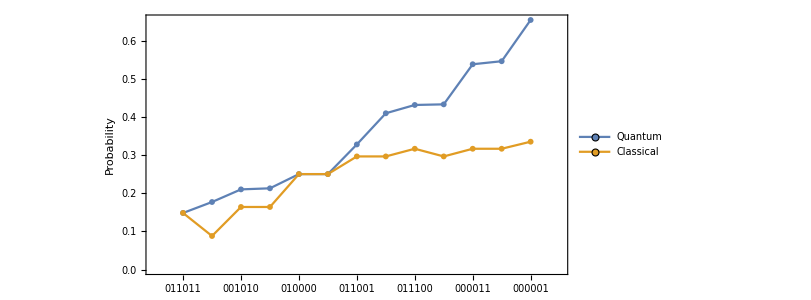

D:\Dropbox\LVB\Dropbox\work\survey\quantum_violations.pdf

```mathematica
pltdata=Select[Table[
d=DC[seq]-1;
If[d>1,
tmp=data[L][d][seq];
{seq,tmp[[3+1]],ComputeProbability[ImportTModel[seq,d],seq]}
],
{seq,IntegerDigits[Range[1,2^(L-1)-1],2,L]}
],#=!=Null&];
pltdata=SortBy[pltdata,#[[2]]&];
pltdata=Select[pltdata,#[[2]]>#[[3]]&];

plt=ListPlot[{
pltdata[[All,3]],
pltdata[[All,2]]
},
Joined->True,
PlotMarkers->{Graphics[{Disk[]}],6},
GridLines->{Range[1,Length[pltdata]],{0,{1/E,Directive[Blue,AbsoluteThickness[1.2]]}}},
Frame->True,
PlotRange->{{0,Length[pltdata]+1},Automatic},
FrameTicks->{{Automatic,{{1/E,"1/e"}}},{
{
#[[1]],
Rotate[Style[StringRiffle[Map[ToString,#[[2]]],""],FontFamily->"Lucida Sans Console"],Pi/2]
}&/@Thread[{Range[1,Length[pltdata]],pltdata[[All,1]]}]
,
None
(*{#[[1]],DC[#[[2]]]}&/@Thread[{Range[1,Length[pltdata]],pltdata[[All,1]]}]*)

}},
FrameLabel->{{"Probability",None},{None,None}},
AspectRatio->1/2,ImageSize->600,
PlotLegends->Placed[{"Classical""Quantum"},Top],
LabelStyle->{14,FontFamily->"Cambria"}
]

Export[NotebookDirectory[]<>"quantum_violations.pdf",plt]

(*ListLinePlot[
pltdata[[All,2]],
ImageSize->400,Joined->False,
PlotLabel->"p(quantum) - p(classical)",
PlotMarkers-> {Graphics[{Disk[]}],7},
GridLines->{Range[1,2^(L-1)-1],Automatic},
PlotRange->All,LabelStyle->12,
Frame->True,FrameTicks->{{Automatic,None},{
Thread[{
Range[1,Length[pltdata]],
StringRiffle[Map[ToString,#],""]&/@pltdata[[All,1]]
}],None}}
],
{x,1,1},{m,{3}}
]//TableForm*)
```

```mathematica
Map[MatrixForm,Round[CanonicalOrder[ImportTModel[#,DC[#]-1],#],0.001]]&/@pltdata[[All,1]]//TableForm
```

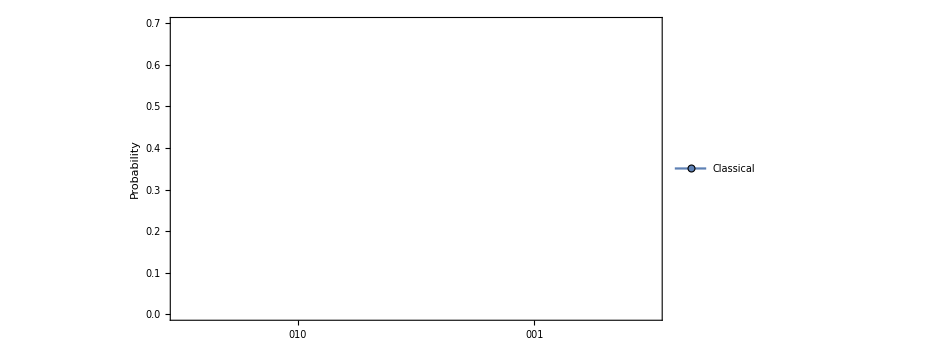

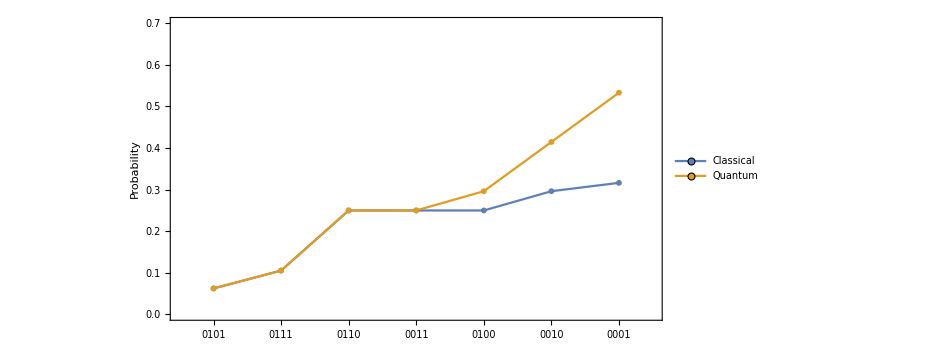

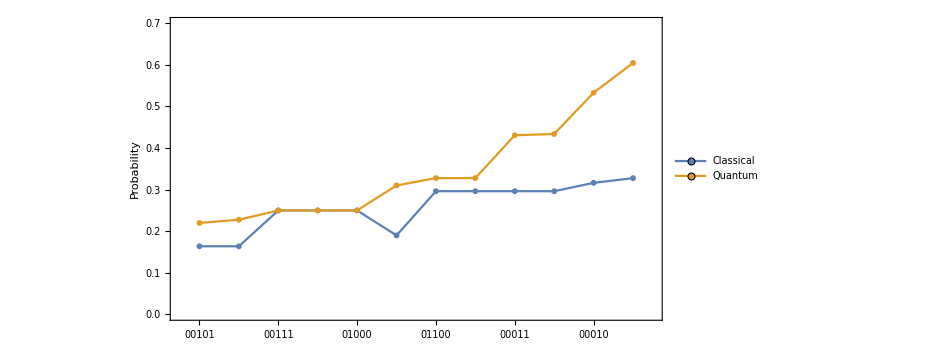

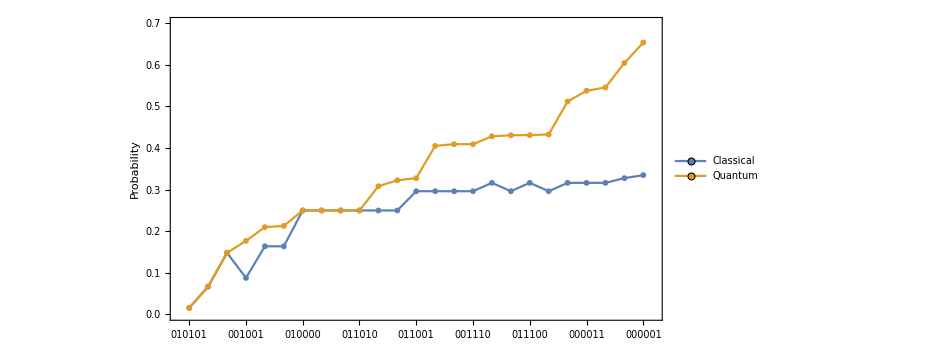

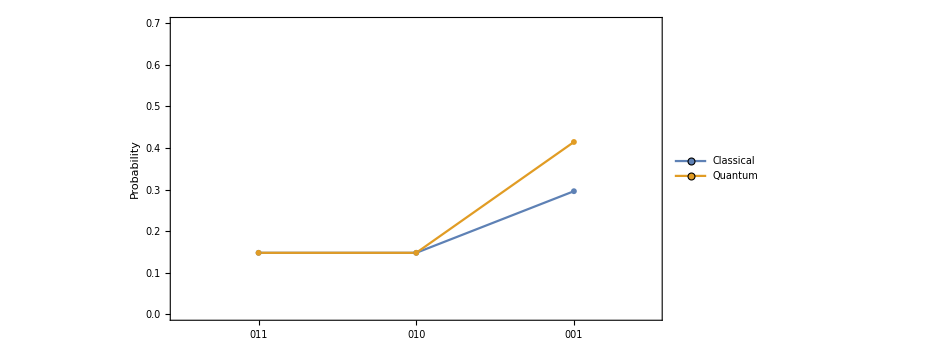

-Graphics-

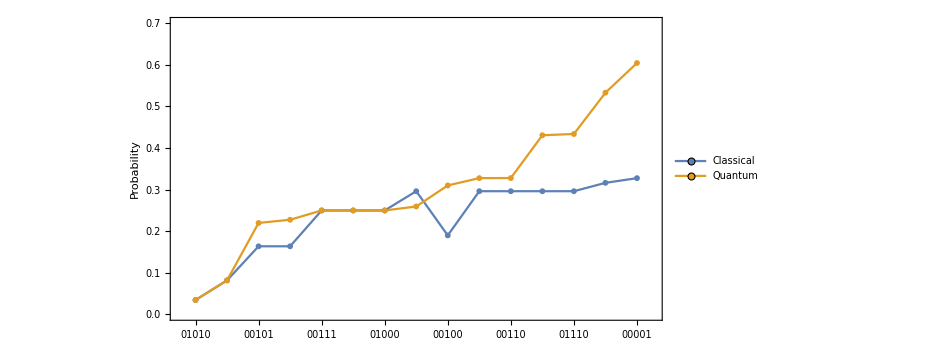

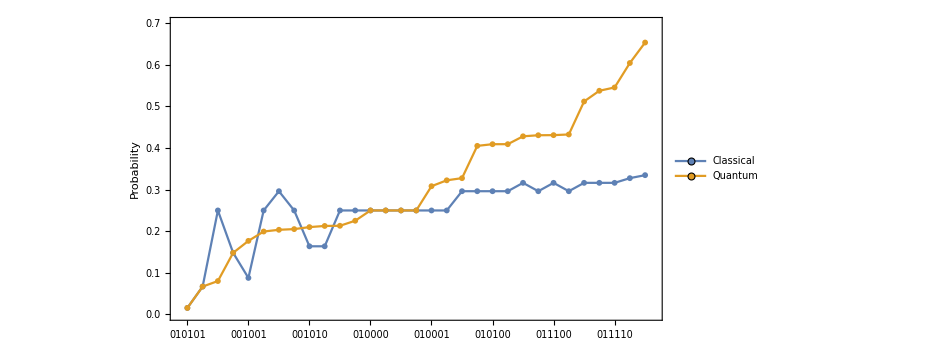

```mathematica
rawdata=Import[NotebookDirectory[]<>"quantumopts.mx"];

Do[

seqs=Keys[rawdata[L]];
data=Select[SortBy[Table[
{
seq,
ComputeProbability[ImportTModel[seq,DC[seq]-1],seq],
rawdata[L][seq][[3]]
},
{seq,seqs}
],{Max[#[[3]]],#[[2]]}&],#[[2]]≤#[[3,1]]&];

plt=ListPlot[{
data[[All,2]],
data[[All,3,1]]
},
Joined->True,
PlotMarkers->{Graphics[{Disk[]}],6},
GridLines->{Range[1,Length[data]],
Join[Range[0,1,0.1],{{1/E,Directive[Blue,AbsoluteThickness[2]]}}]
},
Frame->True,
PlotRange->{{0.5,Length[data]+0.5},{0,0.7}},
FrameTicks->{{Automatic,{{1/E,"1/e"}}},{
{
#[[1]],
Rotate[Style[StringRiffle[Map[ToString,#[[2]]],""],FontFamily->"Lucida Sans Console"],Pi/2]
}&/@Thread[{Range[1,Length[data]],data[[All,1]]}]
,
None
}},
FrameLabel->{{"Probability",None},{None,None}},
AspectRatio->1/2,ImageSize->700,
PlotLegends->Placed[{"Classical","Quantum"},Top],
LabelStyle->{16,FontFamily->"Cambria"}
];
Print[plt];
Export[NotebookDirectory[]<>"quantum_model_onlyviolations_L"<>ToString[L]<>".pdf",plt]
,
{L,3,6}
]

Do[

seqs=Keys[rawdata[L]];
data=SortBy[Table[
{
seq,
ComputeProbability[ImportTModel[seq,DC[seq]-1],seq],
rawdata[L][seq][[3]]
},
{seq,seqs}
],{Max[#[[3]]],#[[2]]}&];

plt=ListPlot[{
data[[All,2]],
data[[All,3,1]]
},
Joined->True,
PlotMarkers->{Graphics[{Disk[]}],6},
GridLines->{Range[1,Length[data]],
Join[Range[0,1,0.1],{{1/E,Directive[Blue,AbsoluteThickness[2]]}}]
},
Frame->True,
PlotRange->{{0.5,Length[data]+0.5},{0,0.7}},
FrameTicks->{{Automatic,{{1/E,"1/e"}}},{
{
#[[1]],
Rotate[Style[StringRiffle[Map[ToString,#[[2]]],""],FontFamily->"Lucida Sans Console"],Pi/2]
}&/@Thread[{Range[1,Length[data]],data[[All,1]]}]
,
None
}},
FrameLabel->{{"Probability",None},{None,None}},
AspectRatio->1/2,ImageSize->700,
PlotLegends->Placed[{"Classical","Quantum"},Top],
LabelStyle->{16,FontFamily->"Cambria"}
];
Print[plt];
Export[NotebookDirectory[]<>"quantum_model_L"<>ToString[L]<>".pdf",plt]
,
{L,3,6}
]
```

## Quantum bound

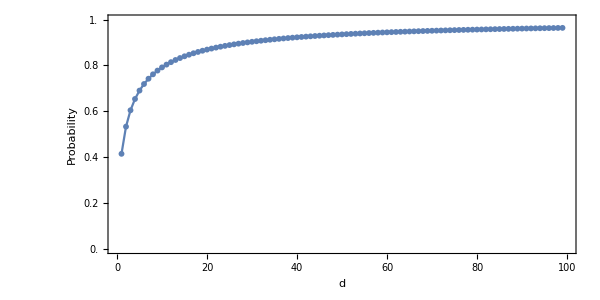

D:\Dropbox\LVB\Dropbox\work\survey\quantum_bound.pdf

```mathematica
plt=ListPlot[
maxpfixed,
Joined->True,
PlotMarkers->{Graphics[{Disk[]}],6},
GridLines->{
Range[0,100,10],
Join[Range[0,1,0.1],{{1/E,Directive[Blue,AbsoluteThickness[2]]},{1,Directive[Red,AbsoluteThickness[2]]}}]
},
Frame->True,
PlotRange->{{0,100},{0,1}},
PlotRangePadding->{0.05,0.05},
FrameTicks->{{Range[0,1,0.2],{{1/E,"1/e"},{1,"1"}}},{Range[0,100,20],None}},
FrameLabel->{{"Probability",None},{"d",None}},
AspectRatio->1/2,ImageSize->600,
LabelStyle->{16,FontFamily->"Cambria"}
]
Export[NotebookDirectory[]<>"quantum_bound.pdf",plt]
```

{0,π}

{0.,0.015851}

{{3,0.533197}}

{{3,2.45736}}

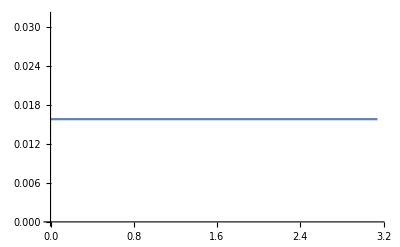

```mathematica
d=3;
q=Sqrt@N[(1-d/(d+1))];
{from,to}={0,Pi}
h=FourierMatrix[d].DiagonalMatrix[N[Range[0,d-1]]].ConjugateTranspose[FourierMatrix[d]];
data=Table[
k0=MatrixExp[ⅈ h (2Pi)/(d+1)].DiagonalMatrix[Map[If[#==d,q,1]&,Range[1,d]]];
{
N[θ],(1-q)Abs[MatrixPower[k0,d][[d,1]]]^2
}
,
{θ,from,to,(to-from)/1000}
];
First[SortBy[data,-#[[2]]&]]
Select[qdata,#[[1]]==d&]
Select[thdata,#[[1]]==d&]
ListLinePlot[
data,
PlotRange->All
]
```

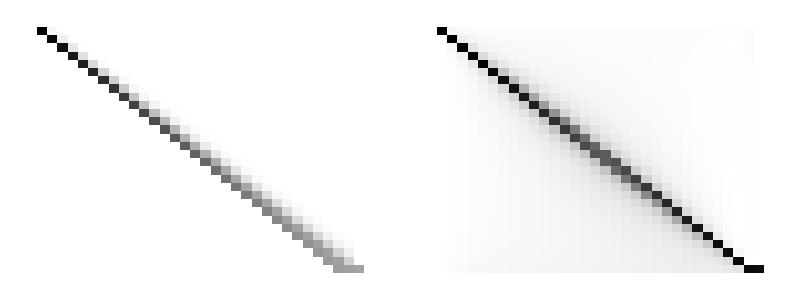

D:\Dropbox\LVB\Dropbox\work\survey\state_evolution.pdf

```mathematica
pq[d_]:=Module[{q,h,k0},
q=Sqrt@N[(1-d/(d+1))];
h=FourierMatrix[d].DiagonalMatrix[N[Range[0,d-1]]].ConjugateTranspose[FourierMatrix[d]];
k0=MatrixExp[-ⅈ h ((2Pi)/(d+1))].DiagonalMatrix[Map[If[#==d,q,1]&,Range[1,d]]];
(1-q^2)Abs[MatrixPower[k0,d][[d,1]]]^2
]
pqhist[d_]:=Module[{q,h,k0,k1,k,rho,hist,s},
q=Sqrt@N[(1-d/(d+1))];
h=FourierMatrix[d].DiagonalMatrix[N[Range[0,d-1]]].ConjugateTranspose[FourierMatrix[d]];
k0=MatrixExp[-ⅈ h ((2Pi)/(d+1))].DiagonalMatrix[Map[If[#==d,q,1]&,Range[1,d]]];
k1=DiagonalMatrix[Map[If[#==d,Sqrt[1-q^2],0]&,Range[1,d]]];
k=IdentityMatrix[d];
(*k1.MatrixPower[k0,d];*)
rho=DiagonalMatrix[Map[KroneckerDelta,Range[0,d-1]]];
hist={rho};
Do[
k={k0,k1}[[s+1]];
rho=k.rho.ConjugateTranspose[k];
AppendTo[hist,rho];
,
{s,IdentityMatrix[d+1][[d+1]]}
];
hist
(*Abs@Tr[k.rho.ConjugateTranspose[k]]*)
]
d=30;
m=N[GeneralizedMulticyclicModel[ConstantArray[1,d],x]/.(#->(1-d/(d+1))&/@Array[x,d])];
plt=TableForm[{{ArrayPlot[
Transpose[
ComputeProbabilityVector[m,ClockSequence[d+1],#]&/@Range[0,d+1]
],
ImageSize->{300,300},
FrameLabel->{{"Time","Classical"},{"State",None}},
LabelStyle->{16,FontFamily->"Cambria"}
],
ArrayPlot[
Transpose[
Re[(Diagonal/@pqhist[30])]^0.5
],
ImageSize->{300,300},
FrameLabel->{{"Time","Quantum"},{None,None}},
LabelStyle->{16,FontFamily->"Cambria"}
]}},TableSpacing->{0,0}]
Export[NotebookDirectory[]<>"state_evolution.pdf",plt]
```

```mathematica
Clear[pq2]
pq2[d_,θ_:0]:=Module[{q,h,k0},
q=Sqrt@N[(1-d/(d+1))];
h=FourierMatrix[d].DiagonalMatrix[N[Range[0,d-1]]].ConjugateTranspose[FourierMatrix[d]];
k0=MatrixExp[-ⅈ h θ].DiagonalMatrix[Map[If[#==d,q,1]&,Range[1,d]]];
(1-q^2)Abs[MatrixPower[k0,d][[d,1]]]^2
]
```

```mathematica
data=Association[Table[d->Table[
{x,pq2[d,x]},
{x,0,2Pi,0.1/d}
],{d,{5,10,15,20}}]];
```

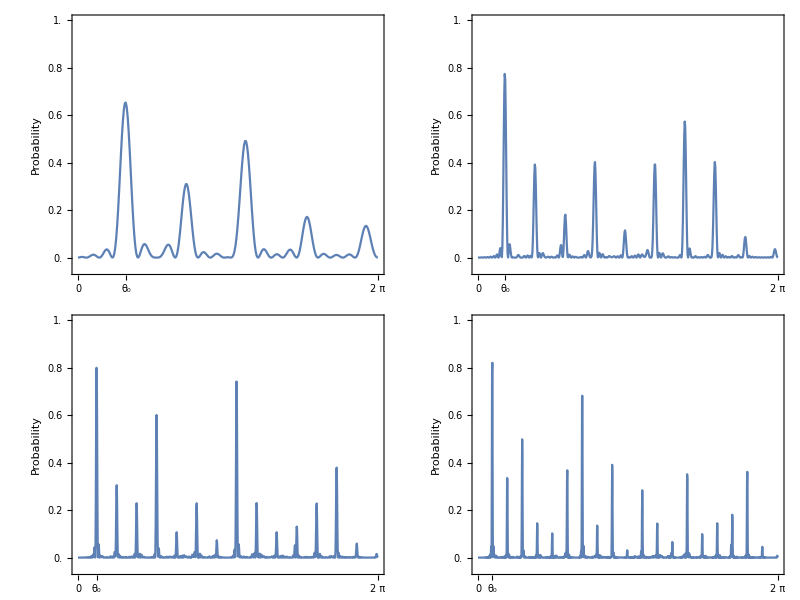

D:\Dropbox\LVB\Dropbox\work\survey\theta_landscape.pdf

```mathematica
plt=ArrayReshape[Table[
ListPlot[
data[d],
PlotRange->{
{0,2Pi},
{-0.05,1}
},
Joined->True,
GridLines->{
Join[Range[0,2Pi,2Pi],{{(2Pi(d-1))/d^2,Directive[Red,AbsoluteThickness[1.5]]}}],
Join[{{0,Directive[Gray,AbsoluteThickness[2]]},{1,Directive[Gray,AbsoluteThickness[2]]}}]
},
Frame->True,
PlotRangePadding->{0.05,0.05},
FrameTicks->{{Range[0,1,0.2],None},{Join[{{(2Pi(d-1))/d^2,"θ_0"}},Range[0,2Pi,2Pi]],None}},
FrameLabel->{{"Probability",None},{None,"d="<>ToString[d]}},
AspectRatio->1/4,ImageSize->600,
LabelStyle->{16,FontFamily->"Cambria"}
],
{d,{5,10,15,20}}
],{2,2}]//TableForm
Export[NotebookDirectory[]<>"theta_landscape.pdf",plt]
```

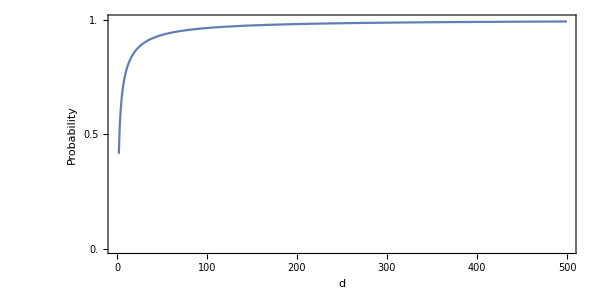

D:\Dropbox\LVB\Dropbox\work\survey\quantum_bound.pdf

```mathematica
plt=ListPlot[
{#[[1]],#[[2]]}&/@Thread[{Range[2,500],BinaryReadList[
FileNameJoin[{NotebookDirectory[],"new_prob_2_500.dat"}]
,"Real32"]}],
Joined->True,
(*PlotMarkers->{Graphics[{Disk[]}],5},*)
GridLines->{
Range[0,500,100],
Join[Range[0,1,0.2],{{1/E,Directive[Blue,AbsoluteThickness[2]]},{1,Directive[Red,AbsoluteThickness[2]]}}]
},
Frame->True,
PlotRange->{{0,500},{0,1}},
PlotRangePadding->{10,0.05},
FrameTicks->{{Range[0,1,0.5],{{1/E,"1/e"},{1,"1"}}},{Range[0,500,100],None}},
FrameLabel->{{"Probability",None},{"d",None}},
AspectRatio->1/2,ImageSize->600,
LabelStyle->{16,FontFamily->"Cambria"}
]
Export[NotebookDirectory[]<>"quantum_bound.pdf",plt]
```